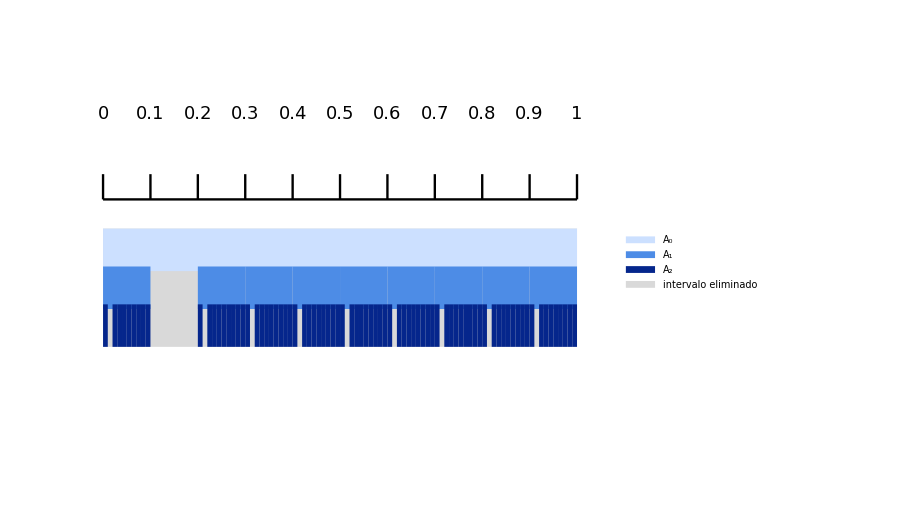

```mathematica
digitosPermitidos={0,2,3,4,5,6,7,8,9}; (*todas las cifras salvo el 1*)

generarIntervalos[0]:={{0,1}};
generarIntervalos[n_]:=Module[{combinaciones=Tuples[digitosPermitidos,n]},Function[digitos,With[{inicio=Sum[digitos[[i]] 10^-i,{i,n}]},{inicio,inicio+10^-n}]]/@combinaciones];

nMax=2;
sep=0.075;    (*separación vertical entre A_n consecutivos*)
axisY=0.1;   (*altura de la recta real:ahora pegada a A_0*)
colores={RGBColor[0.8,0.88,1],RGBColor[0.3,0.55,0.9],RGBColor[0.02,0.15,0.55]};
etiquetas={"A₀","A₁","A₂"};

etiquetasEjeX=Table[Which[k==0,"0",k==10,"1",True,"0."<>ToString[k]],{k,0,10}];

ejeX={Black,Thickness[0.0025],Line[{{0,axisY},{1,axisY}}],Table[Line[{{k/10,axisY},{k/10,axisY+0.05}}],{k,0,10}],Table[Text[Style[etiquetasEjeX[[k+1]],18],{k/10,axisY+0.17}],{k,0,10}]};

fondo=Table[{LightGray,Thickness[0.045],CapForm["Butt"],Line[{{0,-n sep},{1,-n sep}}]},{n,0,nMax}];

barras=Table[Module[{intervalos=generarIntervalos[n],y=-n sep},{colores[[n+1]],Thickness[0.045],CapForm["Butt"],Line[{{#[[1]],y},{#[[2]],y}}]&/@intervalos}],{n,0,nMax}];

grafico=Graphics[{ejeX,fondo,barras},PlotRange->{{-0.05,1.05},{-nMax sep-0.3,axisY+0.3}},ImageSize->680];

imagenFinal=Legended[grafico,SwatchLegend[Append[colores,LightGray],Append[etiquetas,"intervalo eliminado"],LabelStyle->Directive[FontSize->20],LegendMarkerSize->22]];

imagenFinal

Export["problema28_diagrama.png",imagenFinal,ImageResolution->300];
```